# Notebook for computing the spectrum of linearized defocusing MKdV operator.

This notebook computes the spectrum of the linearization about a traveling wave solution to a generalized KdV, in this case MKdV. Specifically we are finding traveling wave solutions to 

in particular the solution , where  solves 
 
in this particular instance the parameter values are , giving a period of roughly     This is the focusing case of MKdV.  
In the code snippet below Abel gives the polynomial in the quadrature . The traveling wave equation is integrated to give the  traveling wave profile. The function Pot(x) returns the potential for the linearized problem.

```mathematica
(* Notebook for computing the spectrum of the linearization around a traveling wave solution to MKdV.*)
(* This generates the traveling wave solutions to gKdV. *)
(* Abel gives the polynomial Subscript[ϕ, x]^2 = Abel[ϕ] giving the solution via quadrature. *)
(* Subscript[u, t] + Subscript[u, xxx] + (u^p)_x = 0 *)
(* p=2 KdV. p=3 MKdV *)
```

```mathematica
p = 3;
c=1;
En = 0;
a = 1/4;
Abel[ϕ_,E_,a_,c_] := 2 E + 2 a ϕ + c ϕ^2 - 2ϕ^(p+1)/(p+1)
RootList=N[x /.Solve[Abel[x,En,a,c]==0,x,Reals,WorkingPrecision->30]];
root2=RootList[[Dimensions[RootList][[1]]]];
root1=RootList[[Dimensions[RootList][[1]]-1]];
avg = (root2+root1)/2;
rad = (root2-root1)/2;
ReducedPoly = PolynomialQuotient[Abel[x,En,a,c],(x-root1)(root2-x),x];
Period = NIntegrate[1/Sqrt[ReducedPoly /. x -> avg + rad Sin[Θ]],{Θ,-Pi,Pi}]
WaveProfile = NDSolve[{y''[x]==a + c y[x] - y[x]^(p)  ,y[0]==root2,y'[0]==0},y,{x,0,2 Period},AccuracyGoal->13,PrecisionGoal->13];
Pot[x_] := Evaluate[(p y[x]^(p-1) - c) /. WaveProfile ][[1]]
```

6.43231

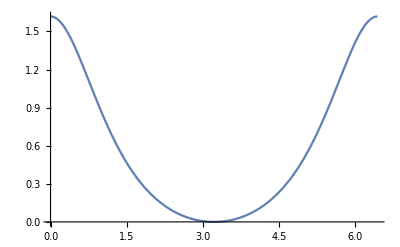

```mathematica
Plot[Evaluate[y[x]/. WaveProfile],{x,0,Period}]
```

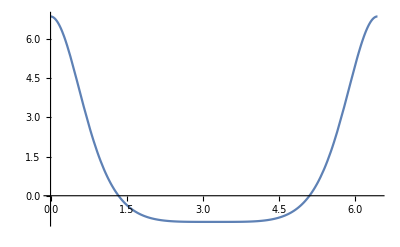

```mathematica
Plot[Pot[x],{x,0,Period}]
```

The code snippet below solves the ODE defining the linearized operator as well as the derivative of this ODE with respect to the eigenvalue parameter λ. This will allow us to generate the monodromy matrix as well as the derivative of the monodromy matrix with respect to the eigenvalue parameter λ. The derivatives are necessary for computing the bifurcation index.

```mathematica
SolMonodromy[l_] := NDSolve[{r1'''[x] + (Pot[x]) r1'[x] - l r1[x]==0,dr1'''[x] + (Pot[x]) dr1'[x] - l dr1[x]-r1[x]==0,r2'''[x] + (Pot[x] ) r2'[x] - l r2[x]==0,dr2'''[x] + (Pot[x] ) dr2'[x] - l dr2[x]- r2[x]==0,r3'''[x] + (Pot[x]) r3'[x] - l r3[x]==0 ,dr3'''[x] + (Pot[x]) dr3'[x] - l dr3[x]-r3[x]==0 ,r1[0]==1,r1'[0]==0,r1''[0]==0,r2[0]==0,r2'[0]==1,r2''[0]==0,r3[0]==0,r3'[0]==0,r3''[0]==1,dr1[0]==0,dr1'[0]==0,dr1''[0]==0,dr2[0]==0,dr2'[0]==0,dr2''[0]==0,dr3[0]==0,dr3'[0]==0,dr3''[0]==0},{r1,r2,r3,dr1,dr2,dr3},{x,0,Period}];
mono[l_] := Evaluate[{{r1[Period],r2[Period],r3[Period]},{r1'[Period],r2'[Period],r3'[Period]},{r1''[Period],r2''[Period],r3''[Period]}}] /. SolMonodromy[l][[1]]
```

The monodromy matrix at λ=0 should have μ=1 as an eigenvalue of geometric multiplicity 2 and algebraic multiplicity 3. The relative error is about .2%.

```mathematica
MatrixForm[mono[0]]
```

(1. | -138.01 | 2.37741×10^-6
0. | 0.999997 | -3.09068×10^-8
0. | 177.507 | 0.999997)

```mathematica
Eigenvalues[%]
```

{1.+0. ⅈ,0.999997+0.00234226 ⅈ,0.999997-0.00234226 ⅈ}

The code snippets below compute the characteristic polynomial of the monodromy matrix (CharPoly[λ]), the complex Floquet discriminant (FloqD), the derivative with respect to λ of the  Floquet discriminant (FloqDp), the discriminant of the characteristic polynomial (Disco) and the bifurcation index (BifIndex)

```mathematica
CharPoly[l_] := CharacteristicPolynomial[mono[l] , μ ];
MonoRoots[l] := μ /. Solve[CharPoly[l]==0,μ];
FloqD[l_] := (Evaluate[r1[Period] + r2'[Period] + r3''[Period]]/. SolMonodromy[l])[[1]]
FloqDp[l_] := (Evaluate[dr1[Period] + dr2'[Period] + dr3''[Period]]/. SolMonodromy[l])[[1]]
Disco[λ_] := Evaluate[(-27-4 Conjugate[r1[Period]+r2'[Period]+r3''[Period]]^3+18 Conjugate[r1[Period]+r2'[Period]+r3''[Period]] (r1[Period]+r2'[Period]+r3''[Period])+Conjugate[r1[Period]+r2'[Period]+r3''[Period]]^2 (r1[Period]+r2'[Period]+r3''[Period])^2-4 (r1[Period]+r2'[Period]+r3''[Period])^3)]/. SolMonodromy[λ][[1]]
BifIndex[l_] := Module[{FF = FloqD[l],FP=FloqDp[l],FPC = Conjugate[FP]},FP^3 + Conjugate[FP]^3 + FF FP Conjugate[FP]^2 + Conjugate[FF] Conjugate[FP] FP^2 ]
```

The plot below depicts the bifurcation index along the imaginary axis (by symmetry this is a real quantity for λ purely imaginary. The plot is turned 90° so that we can see that there are no roots of the bifurcation index other than λ=0.

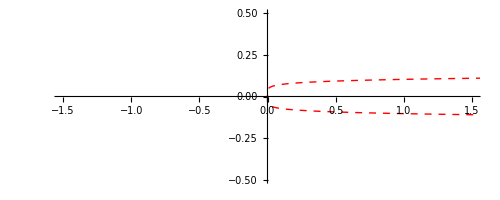

```mathematica
BifIndexPlot=ParametricPlot[{BifIndex[I l],l},{l,-.5,0.50},PlotRange->{{-1.5,1.5},{-0.5,0.5}},PlotStyle->{Red,Thick,Dashed}]
```

```mathematica
Plot[Re[Disco[I r]],{r,0,6}]
```

-Graphics-

```mathematica
Mult[lll_] := If[Disco[lll]<0,.02,.05I]
```

```mathematica
Mult[0.1I]
```

0.005

```mathematica
Mult[.5I]
```

0.+0.005 ⅈ

```mathematica
MultiplicityGraph1=ParametricPlot[{Mult[I l],l},{l,-1.5,1.5},PlotStyle->Magenta,PlotRange->{{-.5,.5},{-1.5,1.5}}];
MultiplicityGraph2=ParametricPlot[{-Mult[I l],l},{l,-1.5,1.5},PlotStyle->Magenta,PlotRange->{{-.5,.5},{-1.5,1.5}}];
```

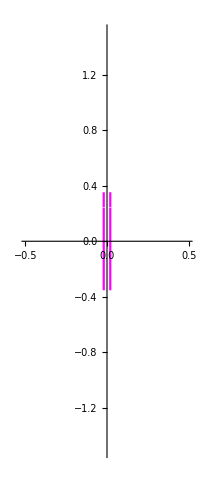

```mathematica
MultiPlot=Show[MultiplicityGraph1,MultiplicityGraph2]
```

```mathematica
(* Deltoid = Locus of points where the (complex) Floquet discriminant has three eigenvalues on the unit circle along the imaginary axis *)
```

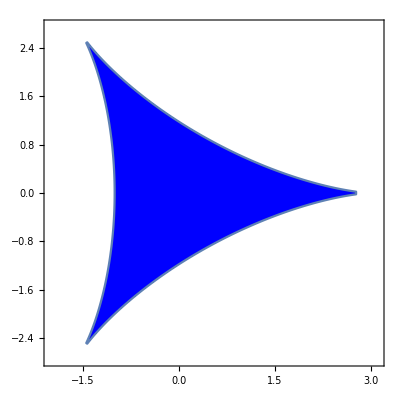

```mathematica
Deltoid1=RegionPlot[-27+18 a^2-8 a^3+a^4+18 b^2+24 a b^2+2 a^2 b^2+b^4<0,{a,-3,3.5},{b,-3.25,3.25},PlotPoints->100,PlotRange->{{-2,3.1},{-2.75,2.75}},PlotStyle->Blue]
```

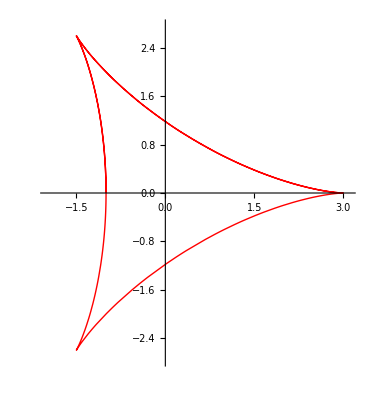

```mathematica
(* This is the Cartesian *)
Astroid[a_,b_,r_] := ParametricPlot[ -r{(a-b) Cos[t] + b Cos[(a-b)/b t],(a-b) Sin[t] + b Sin[(a-b)/b t]},{t,0,6Pi},PlotStyle->{Thick,Red},PlotRange->{{-2,3.1},{-2.75,2.75}}]  
Deltoid2=Astroid[1,2,1]
```

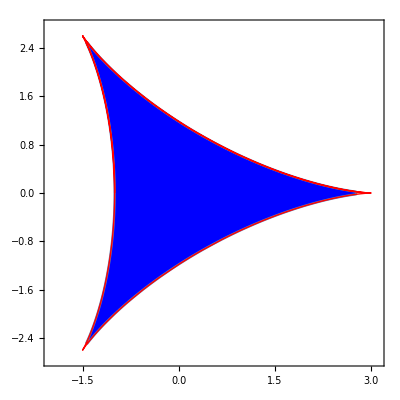

```mathematica
Deltoid3=Show[Deltoid1,Deltoid2]
```

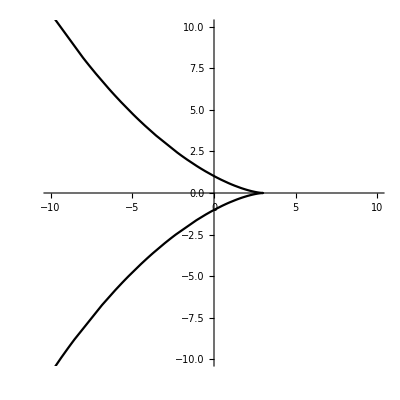

```mathematica
FDPlot=ParametricPlot[{Re[FloqD[I λ]],Im[FloqD[I λ]]},{λ,-10,10},PlotRange->{{-10,10},{-10,10}},PlotStyle->Black]
```

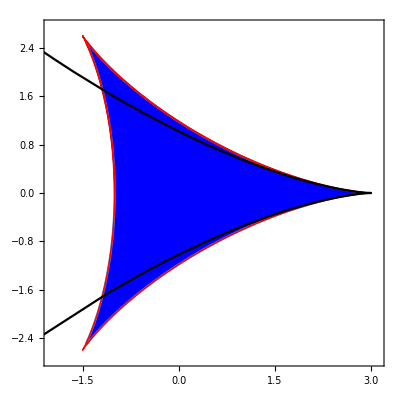

```mathematica
Delt2=Show[Deltoid3,FDPlot]
```

```mathematica
L = Period;
NM = 25;
dx = L/NM;diag = Table[2*Pi*I*1.0(NM-j)/Period,{j,1,2*NM+1}];D1=DiagonalMatrix[diag];
FM = Table[NIntegrate[Exp[2 Pi I k x/Period] Pot[x]/Period,{x,0,Period},AccuracyGoal->15],{k,-2*NM,2*NM}];
FCol = Table[FM[[2NM+2-i]],{i,1,2*NM+1}];
FRow = Table[FM[[i]],{i,2*NM+1,4*NM+1}];
Pot2[x_] := Re[Sum[FM[[k]] Exp[2 Pi I (k-(2*NM+1)) x/Period],{k,1,4*NM+1}]];
PotM = ToeplitzMatrix[Re[FCol],Re[FRow]];
D3=D1.D1.D1;D2=D1.D1;D0=IdentityMatrix[2NM+1];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.58594×10^-13-1.39833×10^-14 ⅈ and 2.93638×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.2641734579766409486095341174125698761047031579152211122618609807}. NIntegrate obtained -1.63636×10^-13-1.28328×10^-14 ⅈ and 3.54228×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.3725324352875406664592134086608914093078281579152211122618609807}. NIntegrate obtained -1.69271×10^-13-7.42088×10^-15 ⅈ and 3.09839×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.3905922654871699516749089332103701873718593420847788877381390194}. NIntegrate obtained -1.82555×10^-13-1.23525×10^-14 ⅈ and 3.3696×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.20094×10^-13-1.11815×10^-14 ⅈ and 3.26233×10^-15 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.32355×10^-13-1.17402×10^-14 ⅈ and 1.94257×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

Eig[q] and Eig2[q] compute the spectrum with quasi-periodic boundary conditions v(L) = exp(2 π i q/L) v(0). Eig computes the spectrum of the linearized operator and Eig2 computes the spectrum of the adjoint. These should be isospectral. At q=0 both show have a triple eigenvalue of 0. In both cases the zero eigenvalues of of order 2 x10^-5

```mathematica
Eig[q_] := Eigenvalues[D3 - 3I q D2 -3q^2 D1 + I q^3 D0 +  PotM.(D1 - I q D0)];
Eig2[q_] := Eigenvalues[D3 - 3I q D2 -3q^2 D1 + I q^3 D0 + (D1 - I q D0). PotM];
```

```mathematica
Chop[Eig[0.0]]
Chop[Eig2[0.0]]
```

{0.+16358.7 ⅈ,0.+14540.3 ⅈ,0.-12863.5 ⅈ,0.+12862.5 ⅈ,0.-11319.2 ⅈ,0.+11319. ⅈ,0.-9904.17 ⅈ,0.+9904.15 ⅈ,0.-8612.32 ⅈ,0.+8612.32 ⅈ,0.-7437.93 ⅈ,0.+7437.93 ⅈ,0.-6375.39 ⅈ,0.+6375.39 ⅈ,0.-5419.1 ⅈ,0.+5419.1 ⅈ,0.-4563.47 ⅈ,0.+4563.47 ⅈ,0.-3802.9 ⅈ,0.+3802.9 ⅈ,0.-3131.82 ⅈ,0.+3131.82 ⅈ,0.-2544.62 ⅈ,0.+2544.62 ⅈ,0.-2035.71 ⅈ,0.+2035.71 ⅈ,0.-1599.51 ⅈ,0.+1599.51 ⅈ,0.+1230.4 ⅈ,0.-1230.4 ⅈ,0.+922.82 ⅈ,0.-922.82 ⅈ,0.-671.157 ⅈ,0.+671.157 ⅈ,0.-469.826 ⅈ,0.+469.826 ⅈ,0.+313.232 ⅈ,0.-313.232 ⅈ,0.-195.785 ⅈ,0.+195.785 ⅈ,0.-111.892 ⅈ,0.+111.892 ⅈ,0.-55.9595 ⅈ,0.+55.9595 ⅈ,0.-22.3966 ⅈ,0.+22.3966 ⅈ,0.-5.61057 ⅈ,0.+5.61057 ⅈ,-8.23032×10^-10+0.0000254982 ⅈ,8.2298×10^-10-0.0000254982 ⅈ,0}

{0.+16358.7 ⅈ,0.+14540.3 ⅈ,0.-12863.5 ⅈ,0.+12862.5 ⅈ,0.-11319.2 ⅈ,0.+11319. ⅈ,0.-9904.17 ⅈ,0.+9904.15 ⅈ,0.-8612.32 ⅈ,0.+8612.32 ⅈ,0.-7437.93 ⅈ,0.+7437.93 ⅈ,0.-6375.39 ⅈ,0.+6375.39 ⅈ,0.-5419.1 ⅈ,0.+5419.1 ⅈ,0.-4563.47 ⅈ,0.+4563.47 ⅈ,0.-3802.9 ⅈ,0.+3802.9 ⅈ,0.-3131.82 ⅈ,0.+3131.82 ⅈ,0.-2544.62 ⅈ,0.+2544.62 ⅈ,0.-2035.71 ⅈ,0.+2035.71 ⅈ,0.+1599.51 ⅈ,0.-1599.51 ⅈ,0.+1230.4 ⅈ,0.-1230.4 ⅈ,0.-922.82 ⅈ,0.+922.82 ⅈ,0.-671.157 ⅈ,0.+671.157 ⅈ,0.+469.826 ⅈ,0.-469.826 ⅈ,0.-313.232 ⅈ,0.+313.232 ⅈ,0.+195.785 ⅈ,0.-195.785 ⅈ,0.-111.892 ⅈ,0.+111.892 ⅈ,0.-55.9595 ⅈ,0.+55.9595 ⅈ,0.-22.3966 ⅈ,0.+22.3966 ⅈ,0.-5.61057 ⅈ,0.+5.61057 ⅈ,1.6782×10^-10+0.0000254978 ⅈ,-1.67789×10^-10-0.0000254978 ⅈ,0}

```mathematica
frame=Plot[0,{x,-1.5,1.5},PlotRange->{-.5,.5}];
l = {}
Do[l=Join[l,Eig[Q]],{Q,-.5,.5,.0001}]
Dimensions[l]
```

{}

{510051}

Find the largest real part.

```mathematica
Max[Re[l]]
```

8.2298×10^-10

```mathematica
Figure4= Show[frame,ComplexListPlot[l,PlotStyle->{Blue,PointSize[Small]}],MultiPlot]
```

-Graphics-

```mathematica
Export["~/Dropbox/Jared Robby/Schmoopys/KdV/Figure4.pdf",Figure4]
```

~/Dropbox/Jared Robby/Schmoopys/KdV/Figure4.pdf

```mathematica
Export["~/Dropbox/Jared Robby/Schmoopys/KdV/Figure4.png",Figure4]
```

~/Dropbox/Jared Robby/Schmoopys/KdV/Figure4.png